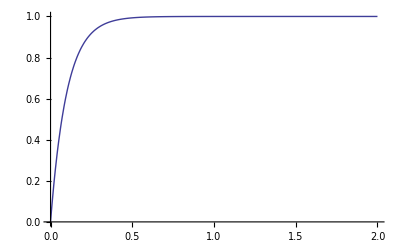

```mathematica
a1 = 0.1;
u[t_] = UnitStep[t];
H[s_] = TransferFunctionModel[1/(1+a1*s),s];
G[z_] = ToDiscreteTimeModel[H[s],1,z];
U[s_] = LaplaceTransform[u[t],t,s];
OutputResponse[H[s],u[t],t];
Plot[%,{t,0,2},PlotRange->All]
```